Интерполационни сплайни - линеен сплайн

```mathematica
Clear[x,y,n,a,b,g,t,z]
x={3.,4.5,7.,9.};   (* таблица за х *)
y={2.5,1.,2.5,0.5}; (* таблица за у *)
(*x={0.,1,2.,3.,4};   (* таблица за х *)
y={1.2,1.3,1.6,1.2,0.6}; (* таблица за у *)*)
n=Length[x]-1;
g1=ListPlot[Table[{x[[i]],y[[i]]},{i,1,n+1}],PlotStyle->Red];
a=b=y;g=y;
For[i=1,i≤n,i++,b[[i]]=(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])];
z=8;
For[j=1,j≤n,j++,
If[x[[j]]≤z&&z≤x[[j+1]],yy=a[[j]]+b[[j]]*(z-x[[j]])];
];
Print["Таблицата с линейните сплайни е:"]
For[k=1,k≤n,k++,
f[t_]:=a[[k]]+b[[k]]*(t-x[[k]]);
g[[k]]=Plot[f[t],{t,x[[k]],x[[k+1]]},AxesOrigin->{0,0}];
Print["    интервал: [",x_⟦k⟧,";",x_⟦k+1⟧,"]   f[",k,"] = ",f[t]]
];
Print["Стойността на сплайна в търсената точка z = ",z ," e ",yy]
```

Таблицата с линейните сплайни е:

интервал: [3.;4.5]   f[1] = 2.5-1. (-3.+t)

интервал: [4.5;7.]   f[2] = 1.+0.6 (-4.5+t)

интервал: [7.;9.]   f[3] = 2.5-1. (-7.+t)

Стойността на сплайна в търсената точка z = 8 e 1.5

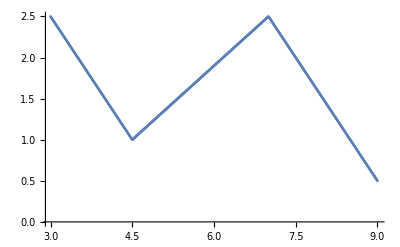

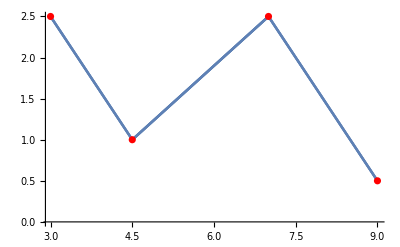

```mathematica
(* графика на сплайна *)
np=1000;hh=(x_⟦n+1⟧-x_⟦1⟧)/np;
p={{x_⟦1⟧,y_⟦1⟧}};
For[i=1,i≤np,i++,xx=x_⟦1⟧+i*hh;
For[k=1,k≤n,k++,If[x_⟦k⟧≤xx && xx≤x_⟦k+1⟧,yy=a[[k]]+b[[k]]*(xx-x[[k]])];];
AppendTo[p,{xx,yy}];
];
g2=ListPlot[p]
Show[g2,g1]
```